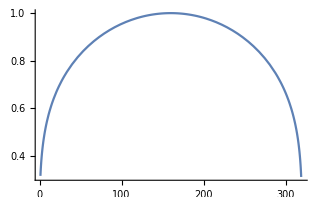

surface temperature

-Graphics-

perfect rectangle

-Graphics-

CheckPoint#2  - excellent

Part::partw: Part 241 of {{0.314774, 0.374326, 0.414252, 0.44513, 0.470651, 0.492578, 0.511905, 0.52925, 0.545029, 0.559533, 0.572977, 0.585523, 0.597298, « 25 », 0.781808, 0.78652, 0.79113, 0.795643, 0.800061, 0.804387, 0.808627, 0.812781, 0.816853, 0.820846, 0.824762, 0.828603, « 270 »}, {« 1 »}, « 47 », {« 20 », « 49 », « 270 »}, « 190 »} does not exist.

$Aborted

noise map

$Aborted

rectangle with noise

$Aborted

```mathematica
ClearAll["Global'*"];
ThermW:=320; ThermH:=240; 
f[x_]:=N[Sqrt@Sqrt[Sin[Pi*(x/ThermW)]]];
Plot[f[y],{y,1,ThermW}]
arx=Array[f[#2]&,{ThermH,ThermW}];
Print["surface temperature"]
ArrayPlot[arx,ImageSize->{Dimensions[arx][[2]],Dimensions[arx][[1]]},ColorFunction->GrayLevel]

For[i=1,i≤Length[arx],i++,{
For[j=1,j≤Length[arx[[i]]],j++,{
If[i≥IntegerPart[ThermH*0.3]&&i≤IntegerPart[ThermH*0.7]&&j≥IntegerPart[ThermW*0.2]&&j≤IntegerPart[ThermW*0.8],arx[[i,j]]:=0.5];
(*If[i≥IntegerPart[ThermH*0.4]&&i≤IntegerPart[ThermH*0.6]&&j≥IntegerPart[ThermW*0.4]&&j≤IntegerPart[ThermW*0.6],arx[[i,j]]:=1];*)

}]
}]
Print["perfect rectangle"]
ArrayPlot[arx,ImageSize->{Dimensions[arx][[2]],Dimensions[arx][[1]]},ColorFunction->GrayLevel]
   (*Begin BLOCK Average*)
memoryTem=0;
mtxw=ThermW; mtxh=ThermH; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

arx2=arx; 
arrenged=Array[{#/#}&,{redw,redh}];
(*subBLOCK NOISE begin*)
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{

arrenged[[i,j]]=Sum[arx2[[Mask43[[i,j,a]]]],{a,sw*sh}]*(1/(sw*sh));
(*noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{arx2[[Mask43[[i,j,a]]]]=(1/TechError)*noiseF[arx2[[Mask43[[i,j,a]]]],arrenged[[i,j]]];
If[Abs@arx2[[Mask43[[i,j,a]]]]>FilterForErrorMagnitude1,arx2[[Mask43[[i,j,a]]]]=0];
arx2[[Mask43[[i,j,a]]]]=Sqrt[(1/(sw*sh))*(TechError*arx2[[Mask43[[i,j,a]]]])^2]; }]    *)
(*Noise block end*)
  }]

}]
(*arrengedList=ArrayReshape[arrenged,{Length[arrenged]*Length[arrenged[[1]]]}]; (*Reshape Matrix List from 1D to 3D*)*)


Clear[arrenged,arrengedList,Mask43];

(*End BLOCK Average*)
NoiseRandom:=RandomReal[{0,0.05},{ThermH,ThermW}];Print["noise map"]
ArrayPlot[NoiseRandom,ImageSize->{Dimensions[NoiseRandom][[2]],Dimensions[NoiseRandom][[1]]},ColorFunction->GrayLevel]
NoisyThermogram:=NoiseRandom+arx;
(*For[i=1,i≤Length[arx],i++,{
For[j=1,j≤Length[arx[[i]]],j++,{
R
}]
}]*)Print["rectangle with noise"]
ArrayPlot[NoisyThermogram,ImageSize->{Dimensions[NoisyThermogram][[2]],Dimensions[NoisyThermogram][[1]]},ColorFunction->GrayLevel]
```

```mathematica
(*Results*)
(*Perfect rect*)
-Graphics-(*binarize*)
-Graphics--Graphics- (*Map:: Local Frac Dimension*) 
-Graphics-(*Spectrum*)
(*Rectangle with noise
*)
-Graphics-(*binarize*)
-Graphics-(*Map:: Local Frac Dimension*) 
-Graphics-(*Legend of D local frac*)

-Graphics-(*Spectrum*)
```

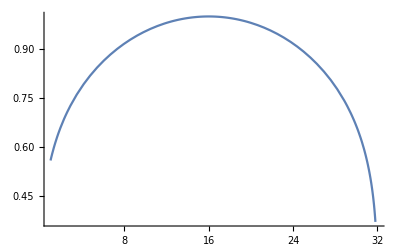

surface temperature

-Graphics-

perfect rectangle

-Graphics-

CheckPoint#2  - excellent

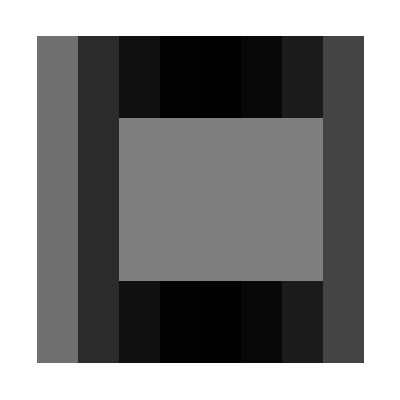

```mathematica
ClearAll["Global'*"];
ThermW:=32; ThermH:=24; 
f[x_]:=N[Sqrt@Sqrt[Sin[Pi*(x/ThermW)]]];
Plot[f[y],{y,1,ThermW}]
arx=Array[f[#2]&,{ThermH,ThermW}];
Print["surface temperature"]
ArrayPlot[arx,ImageSize->{Dimensions[arx][[2]],Dimensions[arx][[1]]},ColorFunction->GrayLevel]

For[i=1,i≤Length[arx],i++,{
For[j=1,j≤Length[arx[[i]]],j++,{
If[i≥IntegerPart[ThermH*0.3]&&i≤IntegerPart[ThermH*0.7]&&j≥IntegerPart[ThermW*0.2]&&j≤IntegerPart[ThermW*0.8],arx[[i,j]]:=0.5];
(*If[i≥IntegerPart[ThermH*0.4]&&i≤IntegerPart[ThermH*0.6]&&j≥IntegerPart[ThermW*0.4]&&j≤IntegerPart[ThermW*0.6],arx[[i,j]]:=1];*)

}]
}]
Print["perfect rectangle"]
ArrayPlot[arx,ImageSize->{Dimensions[arx][[2]],Dimensions[arx][[1]]},ColorFunction->GrayLevel]
   (*Begin BLOCK Average*)
memoryTem=0;
mtxw=ThermW; mtxh=ThermH; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
Mask43=Transpose@ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Flatten[Table[(j-1)*ThermW+i,{i,mtxw},{j,mtxh}]],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]
(*Transpose@Table[(j-1)*ThermW+i,{i,mtxw},{j,mtxh}]//MatrixForm
Transpose@Mask43//MatrixForm*)

arrenged=Array[{#/#}&,{redh,redw}];

(*arx[[IntegerPart[Mask43[[8,8,11]]/(ThermW+1)]+1,
Mask43[[8,8,12]]-IntegerPart[Mask43[[8,8,12]]/(ThermW+1)]*ThermW]]
arx[[24,32]]*)
(*subBLOCK NOISE begin*)
For[ia=1,ia≤redh,ia++,{
For[ja=1,ja≤redw,ja++,{

(*arrenged[[ia,ja]]=Sum[Mask43[[ia,ja,a]],{a,sw*sh}];*)
arrenged[[ia,ja]]=arx[[IntegerPart[Mask43[[ia,ja,1]]/(ThermW)]+1,
Mask43[[ia,ja,1]]-IntegerPart[Mask43[[ia,ja,1]]/(ThermW)]*ThermW]];

}]
}]

ArrayPlot[arrenged]
(*arrenged[[ia,ja]]=Sum[arx[[IntegerPart[Mask43[[ia,ja,a]]/(ThermW+1)]+1,
Mask43[[ia,ja,a]]-IntegerPart[Mask43[[ia,ja,a]]/(ThermW+1)]*ThermW]],{a,sw*sh}]*(1/(sw*sh));*)


(*For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{

arrenged[[i,j]]=Sum[arx2[[,]],{a,sw*sh}]*(1/(sw*sh));

  }]

}]*)
(*arrengedList=ArrayReshape[arrenged,{Length[arrenged]*Length[arrenged[[1]]]}]; (*Reshape Matrix List from 1D to 3D*)*)


Clear[arrenged,Mask43];

(*End BLOCK Average*)
```

```mathematica
bat=Table[l,{k,5},{l,10}]
bat1=Flatten[bat]
bat2=ArrayReshape[bat1,{5,10}]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10}

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

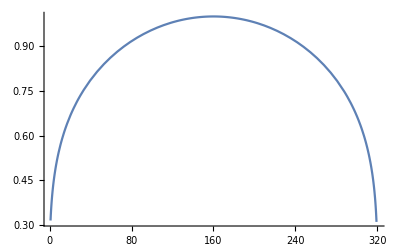

-Graphics3D-

```mathematica
ThermW:=320; ThermH:=240; 
f[x_]:=N[Sqrt@Sqrt[Sin[Pi*(x/ThermW)]]];
Plot[f[y],{y,1,ThermW}]
arx1=ArrayReshape[Array[{#1-0.5,#2-0.5,f[#2]}&,{ThermH,ThermW}],{ThermH*ThermW,3}];
ListPointPlot3D[arx1,PlotStyle->{PointSize[0.05]}]
```

```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
(*Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];*)
(* data1=Import[datafilename1];*)

memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;
f[x_]=N[Sqrt@Sqrt[Sin[Pi*(x/ThermW)]]];
(*Plot[f[y],{y,1,ThermW}]*)
data1=ArrayReshape[Array[{#1-0.5,#2-0.5,f[#2]}&,{mtxh,mtxw}],{mtxh*mtxw,3}];
ImageSizeLocal=450;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};
Dimensions[data1]

(*Begin Rotation script for real thermogram*)
(*For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];(*5*RandomReal[]*(-1)^RandomInteger[1]*);
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem(*5*RandomReal[]*(-1)^RandomInteger[1]*);
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]  *)
 (*End Rotation script for real thermogram*)


(**)

(**)

(*Print the plot of input thermogram*)
ListDensityPlot[data1,PlotRange->All,ColorFunction->colorsGoody(*GrayLevel*),Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True,InterpolationOrder->0] 



(*
(*BLOCK R begin*)
(*Block for reducing the matrix into smaller*)
Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

data2=data1; Clear[data1];
arrenged=Array[{#/#}&,{redw,redh,3}];
(*subBLOCK NOISE begin*)
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-0.5)*sw;
arrenged[[i,j,2]]=sh*(j-0.5);

arrenged[[i,j,3]]=Sum[data2[[Mask43[[i,j,a]],3]],{a,sw*sh}]*(1/(sw*sh));
noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{data2[[Mask43[[i,j,a]],3]]=(1/TechError)*noiseF[data2[[Mask43[[i,j,a]],3]],arrenged[[i,j,3]]];
If[Abs@data2[[Mask43[[i,j,a]],3]]>FilterForErrorMagnitude1,data2[[Mask43[[i,j,a]],3]]=0];
data2[[Mask43[[i,j,a]],3]]=Sqrt[(1/(sw*sh))*(TechError*data2[[Mask43[[i,j,a]],3]])^2]; }]    
(*Noise block end*)
  }]

}]
arrengedList=ArrayReshape[arrenged,{Length[arrenged]*Length[arrenged[[1]]],3}]; (*Reshape Matrix List from 1D to 3D*)

ListDensityPlot[arrengedList,PlotRange->All,ColorFunction->colorsGoody(*GrayLevel*),ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True,InterpolationOrder->0]
Clear[arrenged,arrengedList,Mask43];

(*For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>Temperaturethreshold,data2[[i,3]]=0]]
For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>0.1,data2[[i,3]]=Temperaturethreshold]]*)

ListDensityPlot[data2,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
(*ListPointPlot3D[data1,ColorFunction->Function[{x,y,z},Hue[-z]]]*)
Clear[data2];       
(*subBLOCK NOISE end*)
(*BLOCK R end*)

*)
Print["Joboomba"]
```

{76800,3}

-Graphics-

Joboomba

```mathematica
arrenged=ArrayReshape[Array[{2*#1+#2}&,{5,5,3}],{25,3}]//MatrixForm
```

(3 | 3 | 3
4 | 4 | 4
5 | 5 | 5
6 | 6 | 6
7 | 7 | 7
5 | 5 | 5
6 | 6 | 6
7 | 7 | 7
8 | 8 | 8
9 | 9 | 9
7 | 7 | 7
8 | 8 | 8
9 | 9 | 9
10 | 10 | 10
11 | 11 | 11
9 | 9 | 9
10 | 10 | 10
11 | 11 | 11
12 | 12 | 12
13 | 13 | 13
11 | 11 | 11
12 | 12 | 12
13 | 13 | 13
14 | 14 | 14
15 | 15 | 15)